# Sphere-Sphere

## D. J. Jeffrey and Y. Onishi, J. Fluid Mech., 1984, 139, 261–290.

Here, we consider only equally sized spheres of radius a.  All quantities are scaled by 6 πηa^n with n=1,2,3.

## X_11^A

### Widely Separated (equation 3.13)

```mathematica
X11Aff[s_]:=Module[{λ,f0,f2,f4,f6,f8,f10},
λ=1;
f0=1;
f2=9 λ;
f4=-24 λ+81 λ^2+36 λ^3;
f6=16 λ+108 λ^2+281 λ^3+648 λ^4+144 λ^5;
f8=576 λ^2+4848 λ^3+5409 λ^4+4524 λ^5+3888 λ^6+576 λ^7;
f10=2304 λ^2+20736 λ^3+42804 λ^4+115849 λ^5+76176 λ^6+39264 λ^7+20736 λ^8+2304 λ^9;

f0 +f2 (1+λ)^-2 s^-2+f4(1+λ)^-4 s^-4+f6(1+λ)^-6 s^-6
+f8(1+λ)^-8 s^-8+f10(1+λ)^-10 s^-10];
```

### Nearly Touching

```mathematica
X11Anf[ξ_]:=Module[{λ,g1,g2,g3,A11X},
λ=1;
g1=2 λ^2(1+λ)^-3;
g2=1/5 λ(1+7λ+λ^2)(1+λ)^-3;
g3=1/42(1+18λ-29 λ^2+18 λ^3+λ^4)(1+λ)^-3;
A11X=0.9954;

g1 ξ^-1+g2 Log[ξ^-1]+A11X+g3 ξ Log[ξ^-1] ];
```

### All Separations

```mathematica
X11A[s_]:=Module[{λ,f0,f2,f4,f6,f8,f10,g1,g2,g3},
λ=1;
f0=1;
f2=9 λ;
f4=-24 λ+81 λ^2+36 λ^3;
f6=16 λ+108 λ^2+281 λ^3+648 λ^4+144 λ^5;
f8=576 λ^2+4848 λ^3+5409 λ^4+4524 λ^5+3888 λ^6+576 λ^7;
f10=2304 λ^2+20736 λ^3+42804 λ^4+115849 λ^5+76176 λ^6+39264 λ^7+20736 λ^8+2304 λ^9;
g1=2 λ^2(1+λ)^-3;
g2=1/5 λ(1+7λ+λ^2)(1+λ)^-3;
g3=1/42(1+18λ-29 λ^2+18 λ^3+λ^4)(1+λ)^-3;

g1 (1-4 s^-2)^-1-g2 Log[1-4 s^-2]-g3  (1-4 s^-2) Log[1-4 s^-2] +f0-g1
+(2^-2(1+λ)^-2 f2-g1-2(2)^-1 g2+4 (2)^-1(-2)^-1 g3)(2/s)^2
+(2^-4(1+λ)^-4 f4-g1-2(4)^-1 g2+4 (4)^-1(4-2)^-1 g3)(2/s)^4
+(2^-6(1+λ)^-6 f6-g1-2(6)^-1 g2+4 (6)^-1(6-2)^-1 g3)(2/s)^6
+(2^-8(1+λ)^-8 f8-g1-2(8)^-1 g2+4 (8)^-1(8-2)^-1 g3)(2/s)^8
+(2^-10(1+λ)^-10 f10-g1-2(10)^-1 g2+4 (10)^-1(10-2)^-1 g3)(2/s)^10
+0.0012043398175920273(2/s)^12];
```

```mathematica
Limit[(X11Anf[ξ]-X11A[ξ+2]),ξ->0]
```

0.

### Plot

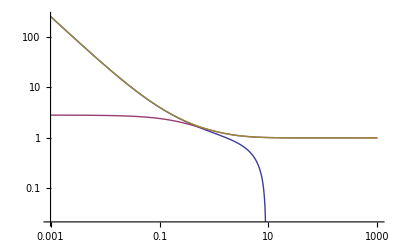

```mathematica
LogLogPlot[{X11Anf[ξ],X11Aff[ξ+2],X11A[ξ+2]},{ξ,10^-3,10^3}]
```

## X_12^A

### Widely Separated

```mathematica
X12Aff[s_]:=Module[{λ,f1,f3,f5,f7,f9,f11},
λ=1;
f1=3λ;
f3=-4λ+27 λ^2-4 λ^3;
f5=72 λ^2+243 λ^3+72 λ^4;
f7=288 λ^2+1620 λ^3+1515 λ^4+1620 λ^5+288 λ^6;
f9=1152 λ^2+9072 λ^3+14752 λ^4+26163 λ^5+14752 λ^6+9072 λ^7+1152 λ^8;
f11=4608 λ^2+46656 λ^3+108912 λ^4+269100 λ^5+319899 λ^6+269100 λ^7+108912 λ^8+46656 λ^9+4608 λ^10;

-2/(1+λ)(f1 (1+λ)^-1 s^-1+f3 (1+λ)^-3 s^-3+f5(1+λ)^-5 s^-5+f7(1+λ)^-7 s^-7
+f9(1+λ)^-9 s^-9+f11(1+λ)^-11 s^-11)];
```

### Nearly Touching

```mathematica
X12Anf[ξ_]:=Module[{λ,g1,g2,g3,A12X},
λ=1;
g1=2 λ^2(1+λ)^-3;
g2=1/5 λ(1+7λ+λ^2)(1+λ)^-3;
g3=1/42(1+18λ-29 λ^2+18 λ^3+λ^4)(1+λ)^-3;
A12X=-0.3502;

-2/(1+λ)(g1 ξ^-1+g2 Log[ξ^-1]-1/2(1+λ)A12X+g3 ξ Log[ξ^-1] )];
```

### All Separations

```mathematica
X12A[s_]:=Module[{λ,f1,f3,f5,f7,f9,f11,g1,g2,g3},
λ=1;
f1=3λ;
f3=-4λ+27 λ^2-4 λ^3;
f5=72 λ^2+243 λ^3+72 λ^4;
f7=288 λ^2+1620 λ^3+1515 λ^4+1620 λ^5+288 λ^6;
f9=1152 λ^2+9072 λ^3+14752 λ^4+26163 λ^5+14752 λ^6+9072 λ^7+1152 λ^8;
f11=4608 λ^2+46656 λ^3+108912 λ^4+269100 λ^5+319899 λ^6+269100 λ^7+108912 λ^8+46656 λ^9+4608 λ^10;
g1=2 λ^2(1+λ)^-3;
g2=1/5 λ(1+7λ+λ^2)(1+λ)^-3;
g3=1/42(1+18λ-29 λ^2+18 λ^3+λ^4)(1+λ)^-3;

-(2/(1+λ))(2 s^-1 g1 (1-4 s^-2)^-1+g2 Log[(s+2)/(s-2)]+g3  (1-4 s^-2) Log[(s+2)/(s-2)] +4 g3 s^-1
+(2^-1(1+λ)^-1 f1-g1-2(1)^-1 g2+4 (1)^-1(1-2)^-1 g3)(2/s)^1
+(2^-3(1+λ)^-3 f3-g1-2(3)^-1 g2+4 (3)^-1(3-2)^-1 g3)(2/s)^3
+(2^-5(1+λ)^-5 f5-g1-2(5)^-1 g2+4 (5)^-1(5-2)^-1 g3)(2/s)^5
+(2^-7(1+λ)^-7 f7-g1-2(7)^-1 g2+4 (7)^-1(7-2)^-1 g3)(2/s)^7
+(2^-9(1+λ)^-9 f9-g1-2(9)^-1 g2+4 (9)^-1(9-2)^-1 g3)(2/s)^9
+(2^-11(1+λ)^-11 f11-g1-2(11)^-1 g2+4 (11)^-1(11-2)^-1 g3)(2/s)^11)
-0.004345303010347383(2/s)^13];
```

```mathematica
Limit[(X12Anf[ξ]-X12A[ξ+2]),ξ->0]
```

0.

### Plot

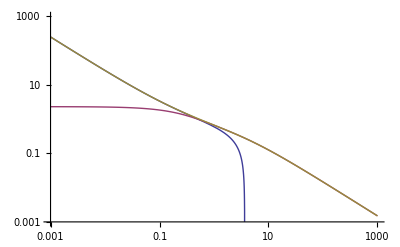

```mathematica
LogLogPlot[{-X12Anf[ξ],-X12Aff[ξ+2],-X12A[ξ+2]},{ξ,10^-3,10^3},PlotRange->{10^-3,1000}]
```

## Y_11^A

### Widely Separated

```mathematica
Y11Aff[s_]:=Module[{λ,f0,f2,f4,f6,f8,f10},
λ=1;
f0=1;
f2=9/4 λ;
f4=6 λ+81/16 λ^2+18 λ^3;
f6=4 λ+54 λ^2+1241/64 λ^3+81 λ^4+72 λ^5;
f8=279 λ^2+4261/8 λ^3+126369/256 λ^4-117/8 λ^5+648 λ^6+288 λ^7;
f10=1152 λ^2+7857/4 λ^3+98487/16 λ^4+10548393/1024 λ^5+67617/8 λ^6-351/2 λ^7+3888 λ^8+1152 λ^9;

f0 +f2 (1+λ)^-2 s^-2+f4(1+λ)^-4 s^-4+f6(1+λ)^-6 s^-6
+f8(1+λ)^-8 s^-8+f10(1+λ)^-10 s^-10];
```

### Nearly Touching

```mathematica
Y11Anf[ξ_]:=Module[{λ,g2,g3,A11Y},
λ=1;
g2=4/15 λ(2+λ+2 λ^2)(1+λ)^-3;
g3=2/375(16-45λ+58 λ^2-45 λ^3+16 λ^4)(1+λ)^-3;
A11Y=0.9983;

g2 Log[ξ^-1]+A11Y+g3 ξ Log[ξ^-1] ];
```

### All Separations

```mathematica
Y11A[s_]:=Module[{λ,f0,f2,f4,f6,f8,f10,g2,g3},
λ=1;
f0=1;
f2=9/4 λ;
f4=6 λ+81/16 λ^2+18 λ^3;
f6=4 λ+54 λ^2+1241/64 λ^3+81 λ^4+72 λ^5;
f8=279 λ^2+4261/8 λ^3+126369/256 λ^4-117/8 λ^5+648 λ^6+288 λ^7;
f10=1152 λ^2+7857/4 λ^3+98487/16 λ^4+10548393/1024 λ^5+67617/8 λ^6-351/2 λ^7+3888 λ^8+1152 λ^9;
g2=4/15 λ(2+λ+2 λ^2)(1+λ)^-3;
g3=2/375(16-45λ+58 λ^2-45 λ^3+16 λ^4)(1+λ)^-3;

-g2 Log[1-4 s^-2]-g3  (1-4 s^-2) Log[1-4 s^-2] +f0
+(2^-2(1+λ)^-2 f2-2(2)^-1 g2+4 (2)^-1(-2)^-1 g3)(2/s)^2
+(2^-4(1+λ)^-4 f4-2(4)^-1 g2+4 (4)^-1(4-2)^-1 g3)(2/s)^4
+(2^-6(1+λ)^-6 f6-2(6)^-1 g2+4 (6)^-1(6-2)^-1 g3)(2/s)^6
+(2^-8(1+λ)^-8 f8-2(8)^-1 g2+4 (8)^-1(8-2)^-1 g3)(2/s)^8
+(2^-10(1+λ)^-10 f10-2(10)^-1 g2+4 (10)^-1(10-2)^-1 g3)(2/s)^10
+0.003115942938956915(2/s)^12];
```

```mathematica
Limit[(Y11Anf[ξ]-Y11A[ξ+2]),ξ->0]
```

0.

### Plot

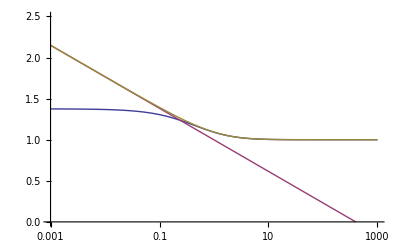

```mathematica
LogLinearPlot[{Y11Aff[ξ+2],Y11Anf[ξ],Y11A[ξ+2]},{ξ,10^-3,10^3},PlotRange->{0,2.5}]
```

## Y_12^A

### Widely Separated

```mathematica
Y12Aff[s_]:=Module[{λ,f1,f3,f5,f7,f9,f11},
λ=1;
f1=3/2 λ;
f3=2λ+27/8 λ^2+2 λ^3;
f5=63/2 λ^2+243/32 λ^3+63/2 λ^4;
f7=144 λ^2+1053/8 λ^3+19083/128 λ^4+1053/8 λ^5+144 λ^6;
f9=576 λ^2+1134 λ^3+60443/32 λ^4+766179/512 λ^5+60443/32 λ^6+1134 λ^7+576 λ^8;
f11=2304 λ^2+7128 λ^3+22071/2 λ^4+2744505/128 λ^5+95203835/2048 λ^6+2744505/128 λ^7+22071/2 λ^8+7128 λ^9+2304 λ^10;

-2/(1+λ)(f1 (1+λ)^-1 s^-1+f3 (1+λ)^-3 s^-3+f5(1+λ)^-5 s^-5+f7(1+λ)^-7 s^-7
+f9(1+λ)^-9 s^-9+f11(1+λ)^-11 s^-11)];
```

### Nearly Touching

```mathematica
Y12Anf[ξ_]:=Module[{λ,g2,g3,A12Y},
λ=1;
g2=4/15 λ(2+λ+2 λ^2)(1+λ)^-3;
g3=2/375(16-45λ+58 λ^2-45 λ^3+16 λ^4)(1+λ)^-3;
A12Y=-0.2737;

-2/(1+λ)(g2 Log[ξ^-1]-1/2(1+λ)A12Y+g3 ξ Log[ξ^-1] )];
```

### All Separations

```mathematica
Y12A[s_]:=Module[{λ,f1,f3,f5,f7,f9,f11,g2,g3},
λ=1;
f1=3/2 λ;
f3=2λ+27/8 λ^2+2 λ^3;
f5=63/2 λ^2+243/32 λ^3+63/2 λ^4;
f7=144 λ^2+1053/8 λ^3+19083/128 λ^4+1053/8 λ^5+144 λ^6;
f9=576 λ^2+1134 λ^3+60443/32 λ^4+766179/512 λ^5+60443/32 λ^6+1134 λ^7+576 λ^8;
f11=2304 λ^2+7128 λ^3+22071/2 λ^4+2744505/128 λ^5+95203835/2048 λ^6+2744505/128 λ^7+22071/2 λ^8+7128 λ^9+2304 λ^10;
g2=4/15 λ(2+λ+2 λ^2)(1+λ)^-3;
g3=2/375(16-45λ+58 λ^2-45 λ^3+16 λ^4)(1+λ)^-3;

-(2/(1+λ))(g2 Log[(s+2)/(s-2)]+g3  (1-4 s^-2) Log[(s+2)/(s-2)] +4 g3 s^-1
+(2^-1(1+λ)^-1 f1-2(1)^-1 g2+4 (1)^-1(1-2)^-1 g3)(2/s)^1
+(2^-3(1+λ)^-3 f3-2(3)^-1 g2+4 (3)^-1(3-2)^-1 g3)(2/s)^3
+(2^-5(1+λ)^-5 f5-2(5)^-1 g2+4 (5)^-1(5-2)^-1 g3)(2/s)^5
+(2^-7(1+λ)^-7 f7-2(7)^-1 g2+4 (7)^-1(7-2)^-1 g3)(2/s)^7
+(2^-9(1+λ)^-9 f9-2(9)^-1 g2+4 (9)^-1(9-2)^-1 g3)(2/s)^9
+(2^-11(1+λ)^-11 f11-2(11)^-1 g2+4 (11)^-1(11-2)^-1 g3)(2/s)^11)
-0.0025700638333700774(2/s)^13];
```

```mathematica
Limit[(Y12Anf[ξ]-Y12A[ξ+2]),ξ->0]
```

0.

### Plot

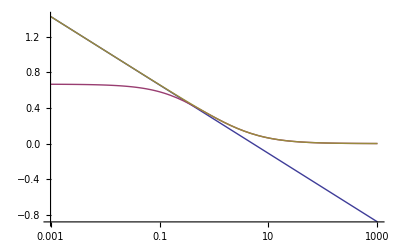

```mathematica
LogLinearPlot[{-Y12Anf[ξ],-Y12Aff[ξ+2],-Y12A[ξ+2]},{ξ,10^-3,10^3}]
```

## Y_11^B

### Widely Separated

```mathematica
Y11Bff[s_]:=Module[{λ,f1,f3,f5,f7,f9,f11},
λ=1;
f1=0;
f3=-9λ;
f5=-12 λ-81/4 λ^2-36 λ^3;
f7=-189 λ^2-8409/16 λ^3-243 λ^4-144 λ^5;
f9=-864 λ^2-3159/4 λ^3-283041/64 λ^4-30525/4 λ^5-1620 λ^6-576 λ^7;
f11=-3456 λ^2-6804 λ^3-614481/16 λ^4-4579497/256 λ^5-536679/16 λ^6-73989 λ^7-9072 λ^8-2304 λ^9;

2/3(f1 (1+λ)^-1 s^-1+f3 (1+λ)^-3 s^-3+f5(1+λ)^-5 s^-5+f7(1+λ)^-7 s^-7
+f9(1+λ)^-9 s^-9+f11(1+λ)^-11 s^-11)];
```

### Nearly Touching

```mathematica
Y11Bnf[ξ_]:=Module[{λ,g2,g3,B11Y},
λ=1;
g2=-1/5 λ(4+λ)(1+λ)^-2;
g3=-1/250(32-33λ+83 λ^2+43 λ^3)(1+λ)^-2;
B11Y=0.2390;

2/3(g2 Log[ξ^-1]+B11Y+g3 ξ Log[ξ^-1] )];
```

### All Separations

```mathematica
Y11B[s_]:=Module[{λ,f1,f3,f5,f7,f9,f11,g2,g3},
λ=1;
f1=0;
f3=-9λ;
f5=-12 λ-81/4 λ^2-36 λ^3;
f7=-189 λ^2-8409/16 λ^3-243 λ^4-144 λ^5;
f9=-864 λ^2-3159/4 λ^3-283041/64 λ^4-30525/4 λ^5-1620 λ^6-576 λ^7;
f11=-3456 λ^2-6804 λ^3-614481/16 λ^4-4579497/256 λ^5-536679/16 λ^6-73989 λ^7-9072 λ^8-2304 λ^9;
g2=-1/5 λ(4+λ)(1+λ)^-2;
g3=-1/250(32-33λ+83 λ^2+43 λ^3)(1+λ)^-2;

2/3(g2 Log[(s+2)/(s-2)]+g3  (1-4 s^-2) Log[(s+2)/(s-2)] +4 g3 s^-1+
+(2^-1(1+λ)^-1 f1-2(1)^-1 g2+4 (1)^-1(1-2)^-1 g3)(2/s)^1
+(2^-3(1+λ)^-3 f3-2(3)^-1 g2+4 (3)^-1(3-2)^-1 g3)(2/s)^3
+(2^-5(1+λ)^-5 f5-2(5)^-1 g2+4 (5)^-1(5-2)^-1 g3)(2/s)^5
+(2^-7(1+λ)^-7 f7-2(7)^-1 g2+4 (7)^-1(7-2)^-1 g3)(2/s)^7
+(2^-9(1+λ)^-9 f9-2(9)^-1 g2+4 (9)^-1(9-2)^-1 g3)(2/s)^9
+(2^-11(1+λ)^-11 f11-2(11)^-1 g2+4 (11)^-1(11-2)^-1 g3)(2/s)^11)
+0.0020899281536625614(2/s)^13];
```

```mathematica
Limit[(Y11Bnf[ξ]-Y11B[ξ+2]),ξ->0]
```

-∞

### Plot

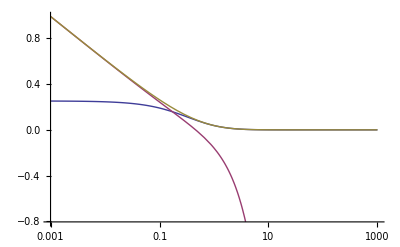

```mathematica
LogLinearPlot[{-Y11Bff[ξ+2],-Y11Bnf[ξ],-Y11B[ξ+2]},{ξ,10^-3,10^3}]
```

## Y_12^B

### Widely Separated

```mathematica
Y12Bff[s_]:=Module[{λ,f0,f2,f4,f6,f8,f10},
λ=1;
f0=0;
f2=-6 λ;
f4=-27/2 λ^2;
f6=-108 λ^2-243/8 λ^3-72 λ^4;
f8=-432 λ^2-486 λ^3-77451/32 λ^4-405 λ^5-288 λ^6;
f10=-1728 λ^2-3888 λ^3-59553/4 λ^4-1125603/128 λ^5-22002 λ^6-2916 λ^7-1152 λ^8;

2/3-4/(1+λ)^2(f0 +f2 (1+λ)^-2 s^-2+f4(1+λ)^-4 s^-4+f6(1+λ)^-6 s^-6
+f8(1+λ)^-8 s^-8+f10(1+λ)^-10 s^-10)];
```

### Nearly Touching

```mathematica
Y12Bnf[ξ_]:=Module[{λ,g2,g3,B12Y},
λ=1;
g2=-1/5 λ(4+λ)(1+λ)^-2;
g3=-1/250(32-33λ+83 λ^2+43 λ^3)(1+λ)^-2;
B12Y=-0.0017;

2/3-4/(1+λ)^2(g2 Log[ξ^-1]+B12Y+g3 ξ Log[ξ^-1] )];
```

### All Separations

```mathematica
Y12B[s_]:=Module[{λ,f0,f2,f4,f6,f8,f10,g2,g3},
λ=1;
f0=0;
f2=-6 λ;
f4=-27/2 λ^2;
f6=-108 λ^2-243/8 λ^3-72 λ^4;
f8=-432 λ^2-486 λ^3-77451/32 λ^4-405 λ^5-288 λ^6;
f10=-1728 λ^2-3888 λ^3-59553/4 λ^4-1125603/128 λ^5-22002 λ^6-2916 λ^7-1152 λ^8;
g2=-1/5 λ(4+λ)(1+λ)^-2;
g3=-1/250(32-33λ+83 λ^2+43 λ^3)(1+λ)^-2;

2/3-4/(1+λ)^2(-g2 Log[1-4 s^-2]-g3  (1-4 s^-2) Log[1-4 s^-2] 
+(2^-2(1+λ)^-2 f2-2(2)^-1 g2+4 (2)^-1(-2)^-1 g3)(2/s)^2
+(2^-4(1+λ)^-4 f4-2(4)^-1 g2+4 (4)^-1(4-2)^-1 g3)(2/s)^4
+(2^-6(1+λ)^-6 f6-2(6)^-1 g2+4 (6)^-1(6-2)^-1 g3)(2/s)^6
+(2^-8(1+λ)^-8 f8-2(8)^-1 g2+4 (8)^-1(8-2)^-1 g3)(2/s)^8
+(2^-10(1+λ)^-10 f10-2(10)^-1 g2+4 (10)^-1(10-2)^-1 g3)(2/s)^10)
+0.0027475923511717055(2/s)^12];
```

```mathematica
Limit[(Y12Bnf[ξ]-Y12B[ξ+2]),ξ->0]
```

0.

### Plot

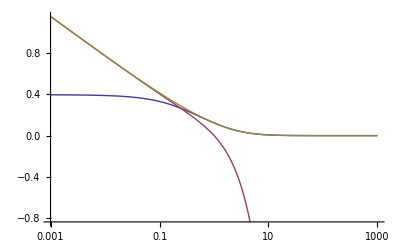

```mathematica
LogLinearPlot[{Y12Bff[ξ+2],Y12Bnf[ξ],Y12B[ξ+2]},{ξ,10^-3,10^3}]
```

## X_11^C

### Widely Separated

```mathematica
X11Cff[s_]:=Module[{λ,f0,f2,f4,f6,f8,f10},
λ=1;
f0=1;
f2=0;
f4=0;
f6=64 λ^3;
f8=768 λ^5;
f10=6144 λ^7;

4/3(f0 +f2 (1+λ)^-2 s^-2+f4(1+λ)^-4 s^-4+f6(1+λ)^-6 s^-6
+f8(1+λ)^-8 s^-8+f10(1+λ)^-10 s^-10)];
```

### Nearly Touching

```mathematica
X11Cnf[ξ_]:=Module[{λ},
λ=1;
4/3(λ^3/(1+λ)^3 Zeta[3,λ/(1+λ)]-λ^2/(4(1+λ))ξ Log[ξ^-1] )];
```

### All Separations (G. B. Jeffrey, Proc. London Math. Soc., 1915, 14, 327–338)

```mathematica
X11C[s_?NumericQ]:=Module[{α,β,n,error,nMax},
α=ArcCosh[s/2];
β=Sinh[α];
error=10^-10;
nMax=Ceiling[-Log[error]/(6α)];
4/3 β^3 NSum[Csch[(2n+1)α]^3,{n,0,nMax},NSumTerms->nMax]];
```

### Plot

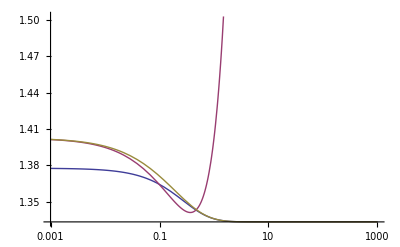

```mathematica
LogLinearPlot[{X11Cff[ξ+2],X11Cnf[ξ],X11C[ξ+2]},{ξ,10^-3,10^3}]
```

## X_12^C

### Widely Separated

```mathematica
X12Cff[s_]:=Module[{λ,f1,f3,f5,f7,f9,f11},
λ=1;
f1=0;
f3=8 λ^3;
f5=0;
f7=0;
f9=512 λ^6;
f11=6144 λ^6+6144 λ^8;

4/3-8/(1+λ)^3(f1 (1+λ)^-1 s^-1+f3 (1+λ)^-3 s^-3+f5(1+λ)^-5 s^-5+f7(1+λ)^-7 s^-7
+f9(1+λ)^-9 s^-9+f11(1+λ)^-11 s^-11)];
```

### Nearly Touching

```mathematica
X12Cnf[ξ_]:=Module[{λ},
λ=1;
4/3((-8 λ^3)/(1+λ)^6 Zeta[3]+(2 λ^2)/(1+λ)^4 ξ Log[ξ^-1] )];
```

### All Separations (G. B. Jeffrey, Proc. London Math. Soc., 1915, 14, 327–338)

```mathematica
X12C[s_?NumericQ]:=Module[{α,β,n,error,nMax},
α=ArcCosh[s/2];
β=Sinh[α];
error=10^-10;
nMax=Ceiling[-Log[error]/(6α)];
-4/3 β^3 NSum[Csch[2(n+1)α]^3,{n,0,nMax},NSumTerms->nMax]];
```

### Plot

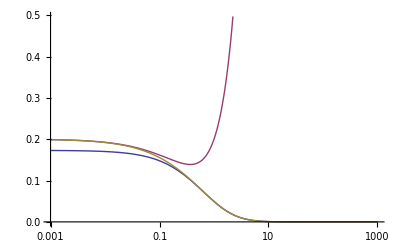

```mathematica
LogLinearPlot[{-X12Cff[ξ+2],-X12Cnf[ξ],-X12C[ξ+2]},{ξ,10^-3,10^3}]
```

## Y_11^C

### Widely Separated

```mathematica
Y11Cff[s_]:=Module[{λ,f0,f2,f4,f6,f8,f10},
λ=1;
f0=1;
f2=0;
f4=12λ;
f6=27 λ^2+256 λ^3;
f8=216 λ^2+243/4 λ^3+216 λ^4+2496 λ^6;
f10=864 λ^2+972 λ^3+151179/16 λ^4+972 λ^5+1296 λ^6+18432 λ^7;

4/3(f0 +f2 (1+λ)^-2 s^-2+f4(1+λ)^-4 s^-4+f6(1+λ)^-6 s^-6
+f8(1+λ)^-8 s^-8+f10(1+λ)^-10 s^-10)];
```

### Nearly Touching

```mathematica
Y11Cnf[ξ_]:=Module[{λ,g2,g3,C11Y},
λ=1;
g2=2/5 λ(1+λ)^-1;
g3=1/125(8+6λ+33 λ^2)(1+λ)^-1;
C11Y=0.7028;

4/3(g2 Log[ξ^-1]+C11Y + g3 ξ Log[ξ^-1] )];
```

### All Separations

```mathematica
Y11C[s_]:=Module[{λ,f0,f2,f4,f6,f8,f10,g2,g3},
λ=1;
f0=1;
f2=0;
f4=12λ;
f6=27 λ^2+256 λ^3;
f8=216 λ^2+243/4 λ^3+216 λ^4+2496 λ^6;
f10=864 λ^2+972 λ^3+151179/16 λ^4+972 λ^5+1296 λ^6+18432 λ^7;
g2=2/5 λ(1+λ)^-1;
g3=1/125(8+6λ+33 λ^2)(1+λ)^-1;

4/3(-g2 Log[1-4 s^-2]-g3  (1-4 s^-2) Log[1-4 s^-2]+f0 
+(2^-2(1+λ)^-2 f2-2(2)^-1 g2+4 (2)^-1(-2)^-1 g3)(2/s)^2
+(2^-4(1+λ)^-4 f4-2(4)^-1 g2+4 (4)^-1(4-2)^-1 g3)(2/s)^4
+(2^-6(1+λ)^-6 f6-2(6)^-1 g2+4 (6)^-1(6-2)^-1 g3)(2/s)^6
+(2^-8(1+λ)^-8 f8-2(8)^-1 g2+4 (8)^-1(8-2)^-1 g3)(2/s)^8
+(2^-10(1+λ)^-10 f10-2(10)^-1 g2+4 (10)^-1(10-2)^-1 g3)(2/s)^10)
+0.006656251992119657(2/s)^12];
```

```mathematica
Limit[(Y11Cnf[ξ]-Y11C[ξ+2]),ξ->0]
```

0.

### Plot

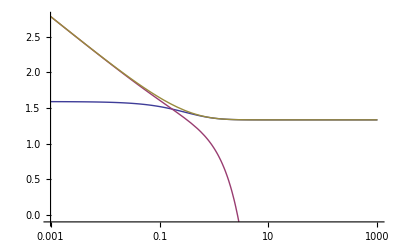

```mathematica
LogLinearPlot[{Y11Cff[ξ+2],Y11Cnf[ξ],Y11C[ξ+2]},{ξ,10^-3,10^3}]
```

## Y_12^C

### Widely Separated

```mathematica
Y12Cff[s_]:=Module[{λ,f1,f3,f5,f7,f9,f11},
λ=1;
f1=0;
f3=4 λ^3;
f5=18 λ^4;
f7=72 λ^4+81/2 λ^5+72 λ^6;
f9=288 λ^4+486 λ^5-6439/8 λ^6+486 λ^7+288 λ^8;
f11=1152 λ^4+3240 λ^5-10947/2 λ^6+518049/32 λ^7-10947/2 λ^8+3240 λ^9+1152 λ^10;

4/3 8/(1+λ)^3(f1 (1+λ)^-1 s^-1+f3 (1+λ)^-3 s^-3+f5(1+λ)^-5 s^-5+f7(1+λ)^-7 s^-7
+f9(1+λ)^-9 s^-9+f11(1+λ)^-11 s^-11)];
```

### Nearly Touching

```mathematica
Y12Cnf[ξ_]:=Module[{λ,g4,g5,C12Y},
λ=1;
g4=4/5 λ^2(1+λ)^-4;
g5=4/125 λ(43-24λ+43 λ^2)(1+λ)^-4;
C12Y=-0.0274;

4/3(1+λ)^3/8(g4 Log[ξ^-1]+C12Y + g5 ξ Log[ξ^-1]/2 )];
```

### All Separations

```mathematica
Y12C[s_]:=Module[{λ,f1,f3,f5,f7,f9,f11,g4,g5},
λ=1;
f1=0;
f3=4 λ^3;
f5=18 λ^4;
f7=72 λ^4+81/2 λ^5+72 λ^6;
f9=288 λ^4+486 λ^5-6439/8 λ^6+486 λ^7+288 λ^8;
f11=1152 λ^4+3240 λ^5-10947/2 λ^6+518049/32 λ^7-10947/2 λ^8+3240 λ^9+1152 λ^10;
g4=4/5 λ^2(1+λ)^-4;
g5=4/125 λ(43-24λ+43 λ^2)(1+λ)^-4;

4/3 8/(1+λ)^3(g4 Log[(s+2)/(s-2)]+g5  (1-4 s^-2) Log[(s+2)/(s-2)]+4 g5 s^-1
+(2^-1(1+λ)^-1 f1-2(1)^-1 g4+4 (1)^-1(1-2)^-1 g5)(2/s)^1
+(2^-3(1+λ)^-3 f3-2(3)^-1 g4+4 (3)^-1(3-2)^-1 g5)(2/s)^3
+(2^-5(1+λ)^-5 f5-2(5)^-1 g4+4 (5)^-1(5-2)^-1 g5)(2/s)^5
+(2^-7(1+λ)^-7 f7-2(7)^-1 g4+4 (7)^-1(7-2)^-1 g5)(2/s)^7
+(2^-9(1+λ)^-9 f9-2(9)^-1 g4+4 (9)^-1(9-2)^-1 g5)(2/s)^9
+(2^-11(1+λ)^-11 f11-2(11)^-1 g4+4 (11)^-1(11-2)^-1 g5)(2/s)^11)
+0.02151177284776819(2/s)^13];
```

```mathematica
Limit[(Y12Cnf[ξ]-Y12C[ξ+2]),ξ->0]
```

0.

### Plot

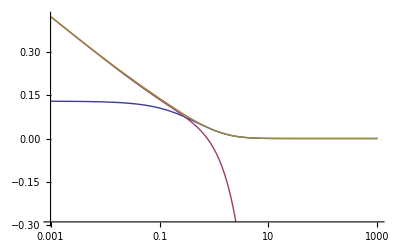

```mathematica
LogLinearPlot[{Y12Cff[ξ+2],Y12Cnf[ξ],Y12C[ξ+2]},{ξ,10^-3,10^3}]
```

## Tabulation Parameters

```mathematica
Npoints = 1000;
ξmin = 10^-3;
ξmax = 10^3;
```

```mathematica
OutputTable=ParallelTable[{2+10^s,X11A[2+10^s],X12A[2+10^s],Y11A[2+10^s],Y12A[2+10^s],
Y11B[2+10^s],Y12B[2+10^s],
X11C[2+10^s],X12C[2+10^s],Y11C[2+10^s],Y12C[2+10^s]},
{s,Log10[ξmin],Log10[ξmax],(Log10[ξmax]-Log10[ξmin])/(Npoints-1)}];
SetDirectory[NotebookDirectory[]];
Export["SphereSphereResistance.txt",N[OutputTable],"TSV"]
```

SphereSphereResistance.txt